## Nucleation Analysis (Multi - stranded)

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

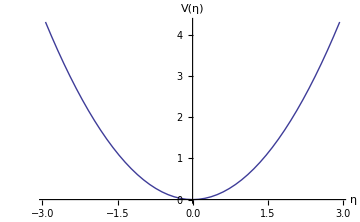

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]

PotentialData = Import["POTENTIAL_DATA","Table"];
PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters","Grid"]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]
```

Numerical Results - MXD

R

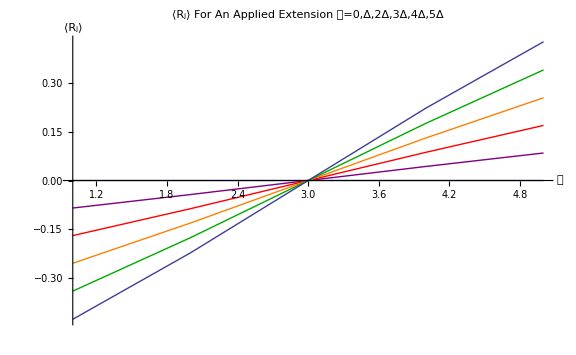

```mathematica
p1=ListLinePlot[Subscript[R, mxd][[1]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[Subscript[R, mxd][[2]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[Subscript[R, mxd][[3]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[Subscript[R, mxd][[4]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[Subscript[R, mxd][[5]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[Subscript[R, mxd][[6]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨R_j⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨R_j⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

ρ

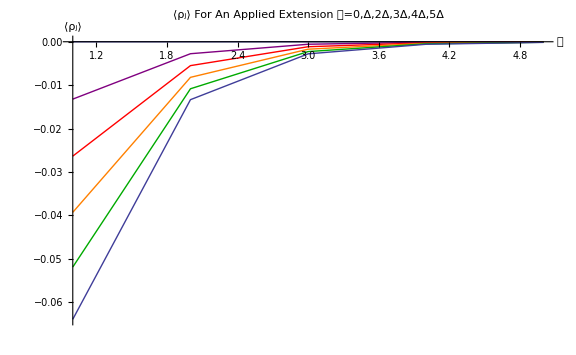

```mathematica
p1=ListLinePlot[Subscript[ρ, mxd][[1]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[Subscript[ρ, mxd][[2]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[Subscript[ρ, mxd][[3]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[Subscript[ρ, mxd][[4]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[Subscript[ρ, mxd][[5]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[Subscript[ρ, mxd][[6]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨ρ_j⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨ρ_j⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

λ

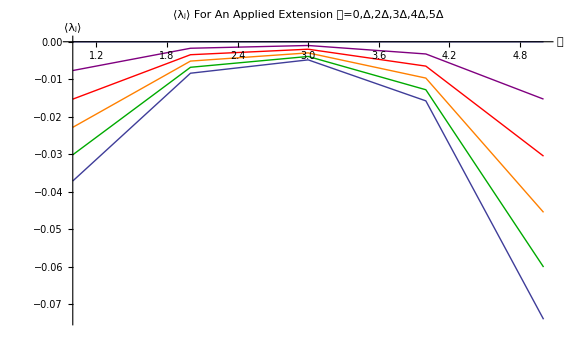

```mathematica
p1=ListLinePlot[Subscript[λ, mxd][[1]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[Subscript[λ, mxd][[2]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[Subscript[λ, mxd][[3]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[Subscript[λ, mxd][[4]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[Subscript[λ, mxd][[5]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[Subscript[λ, mxd][[6]],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨λ_j⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨λ_j⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

Mean Axial Displacement λ''= z + x - 2 y

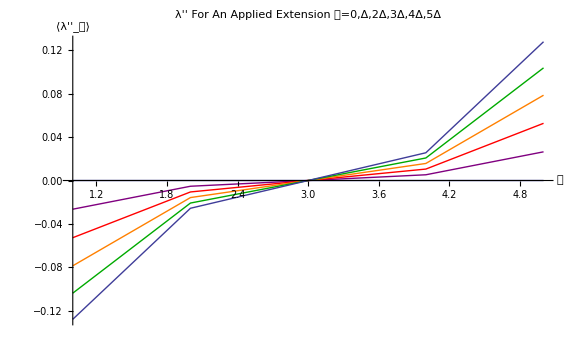

```mathematica
mxd[i_]:=-√3 Subscript[λ, mxd][[i]]+3 Subscript[ρ, mxd][[i]]
p1=ListLinePlot[mxd[1],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[mxd[2],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[mxd[3],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[mxd[4],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[mxd[5],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[mxd[6],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨\!\(\*SubscriptBox[\"λ''\", \"𝒿\"]\)⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["λ'' For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

⟨x_i⟩

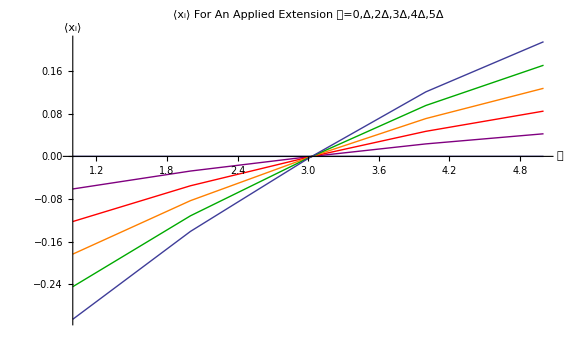

```mathematica
X[i_]:=(Subscript[R, mxd][[i]])/(√3)+(Subscript[λ, mxd][[i]])/(√6)+(Subscript[ρ, mxd][[i]])/(√2)
p1=ListLinePlot[X[1],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[X[2],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[X[3],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[X[4],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[X[5],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[X[6],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨x_i⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨x_i⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

⟨y_i⟩

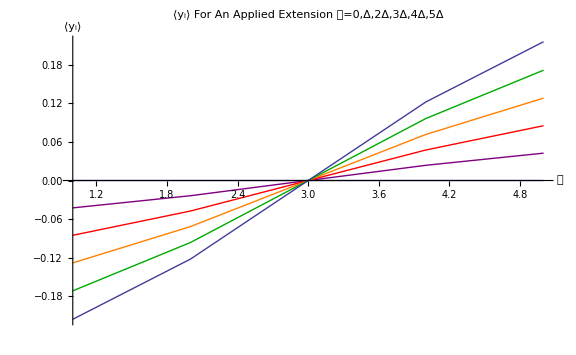

```mathematica
Y[i_]:=(Subscript[R, mxd][[i]])/(√3)+(Subscript[λ, mxd][[i]])/(√6)-(Subscript[ρ, mxd][[i]])/(√2)
p1=ListLinePlot[Y[1],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[Y[2],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[Y[3],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[Y[4],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[Y[5],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[Y[6],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨y_i⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨y_i⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

⟨z_i⟩

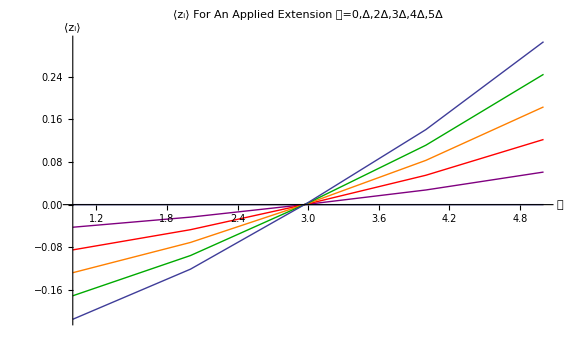

```mathematica
Z[i_]:=(Subscript[R, mxd][[i]])/(√3)-(√2 Subscript[λ, mxd][[i]])/(√3)
p1=ListLinePlot[Z[1],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];
p2=ListLinePlot[Z[2],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Purple,Thick}];
p3=ListLinePlot[Z[3],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Red,Thick}];
p4=ListLinePlot[Z[4],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Orange,Thick}];
p5=ListLinePlot[Z[5],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Darker[Green],Thick}];
p6=ListLinePlot[Z[6],ImageSize->Large,AxesOrigin->{1,0},PlotStyle->{Thick}];

Show[p1,p2,p3,p4,p5,p6,ImageSize->Large,PlotRange->All,AxesLabel->{Style["𝒿",FontSize->18],Style["⟨z_i⟩",FontSize->18]},LabelStyle->{"Times",16},PlotLabel->Style["⟨z_i⟩ For An Applied Extension 𝓊=0,Δ,2Δ,3Δ,4Δ,5Δ",FontSize->16]]
```

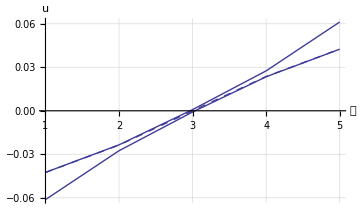
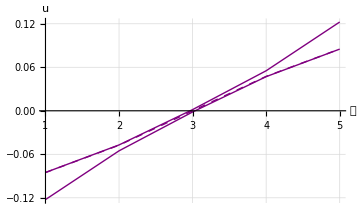
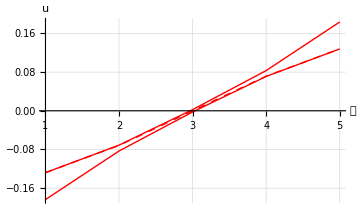
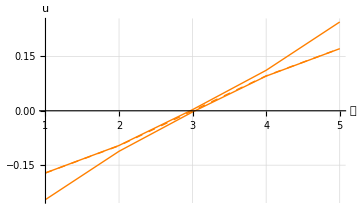

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

{Show[
{ListLinePlot[X[2],PlotStyle->Thick],
ListLinePlot[Y[2],PlotStyle->{Thick,Dashed}],
ListLinePlot[Z[2],PlotStyle->Thick]},
PlotRange->All,
ImageSize->Medium,
AxesOrigin->{1,0},
AxesLabel->{
Style["𝒿",FontSize->18],
Style["u",FontSize->18]
},
LabelStyle->{"Times",16},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed]
],
Show[
{ListLinePlot[X[3],PlotStyle->{Thick,Purple}],
ListLinePlot[Y[3],PlotStyle->{Thick,Dashed,Purple}],
ListLinePlot[Z[3],PlotStyle->{Thick,Purple}]},
PlotRange->All,
ImageSize->Medium,
AxesOrigin->{1,0},
AxesLabel->{
Style["𝒿",FontSize->18],
Style["u",FontSize->18]
},
LabelStyle->{"Times",16},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed]
],
Show[
{ListLinePlot[X[4],PlotStyle->{Thick,Red}],
ListLinePlot[Y[4],PlotStyle->{Thick,Dashed,Red}],
ListLinePlot[Z[4],PlotStyle->{Thick,Red}]},
PlotRange->All,
ImageSize->Medium,
AxesOrigin->{1,0},
AxesLabel->{
Style["𝒿",FontSize->18],
Style["u",FontSize->18]
},
LabelStyle->{"Times",16},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed]
],
Show[
{ListLinePlot[X[5],PlotStyle->{Thick,Orange}],
ListLinePlot[Y[5],PlotStyle->{Thick,Dashed,Orange}],
ListLinePlot[Z[5],PlotStyle->{Thick,Orange}]},
PlotRange->All,
ImageSize->Medium,
AxesOrigin->{1,0},
AxesLabel->{
Style["𝒿",FontSize->18],
Style["u",FontSize->18]
},
LabelStyle->{"Times",16},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed]
]}
```

```mathematica
L=5;
m=20;
Δ=L/(2m+1)//N
```

0.121951

#### The extension at each end is u/2 for an overall extension U

```mathematica
Δ/2
3 Δ/2
5 Δ/2
```

0.0609756

0.182927

0.304878

#### Z strand displacements +u/2

```mathematica
Z[2][[5]]
Z[4][[5]]
Z[6][[5]]
```

0.0612245

0.183673

0.306121

#### X strand displacements -u/2

```mathematica
X[2][[1]]
X[4][[1]]
X[6][[1]]
```

-0.0612245

-0.183673

-0.306121

### Effective factor U/2 for U=Δ,3Δ,5Δ

```mathematica
Δ/2/Z[2][[5]]
3 Δ/2/Z[4][[5]]
5 Δ/2/Z[6][[5]]
```

0.995935

0.995935

0.995939